# Problem rojstnega dne

Recimo, da mečemo kovanec in stavimo, na cifro. Ker je enako verjetno, da pade cifra ali glava je verjetnost da pade cifra torej 50%. Če bi vedno stavili na cifro, to pomeni, da bi načeloma na dolgi rok zmagali polovico metov. 

Kaj pa če bi kdo želel staviti na to, da imata vsaj dva v razredu rojstni dan na isti dan?
Vprašanje je bolj kompleksno kot se zdi. Verjetnost, da imata vsaj dva v skupini ljudi (n) je seveda odvisna od velikosti te skupine. Če sta v skupini samo dva človeka, bi bili verjetno presenečeni, če bi imela na isti dan rojstni dan. Torej kako velika mora biti skupina ljudi (n), da bi verjetnost, da imata vsaj dva na isti dan rojstni dan zrastla na 50%?

Pri tem problemu bomo zanemarili prestopna leta. Predpostavili bomo torej, da je vsako leto dolgo točno 365 dni. Predpostavili bomo tudi, da je vsak dan enako primeren za rojstni dan, kot ostali. 

Začnemo tako, da izračunamo verjetnost, da imata dva človeka na isti dan rojstni dan. Skupina ljudi (n) bo sestavljena torej iz dveh ljudi.
Prvi človek ima lahko katerikoli rojstni dan. Ima 365 možnosti od 365 dni.
Torej je verjetnost (365/365) kar pa je enako 1. Verjetnost, da ima drugi človek na isti dan rojstni dan pa je (1/365), ker ima na voljo samo en specifičen dan. Da izračunamo verjetnost, da imata oba isti rojstni dan moramo verjetnosti med sabo pomnožiti:

```mathematica
P = N[(365/365)*(1/365)];
```

```mathematica
PercentForm[P]
```

0.274%

Verjetnost, da imata v skupini dveh naključno izbranih ljudi oba na isti dan rojstni dan je torej približno 0.274%.
Kaj pa če so v skupini ljudi trije ljudje?
Verjetnost, da imata prva dva rojstni dan na isti dan je torej 1/365. Lahko pa imata skupni rojstni dan tudi prvi in tretji, ali pa imajo rojstni dan vsi trije na isti dan. Stvari se hitro zakomplicirajo.

Da bi rešili problem, moramo poznati eno od osnovnih pravil verjetnosti. To je, da je verjetnost vedno vrednost med 0 in 1 in da je vsota verjetnosti da se dogodek zgodi in verjetnosti da se dogodek ne zgodi vedno enaka 1.

P(dogodek se zgodi) + P(dogodek se ne zgodi) = 1
oziroma:
P(imata vsaj dva skupni rd) + P(nimata niti dva) = 1
iz tega sledi:
P(imata vsaj dva skupni rd) = 1 - P(nimata niti dva)

Kakšna je torej verjetnost, da nimata niti dva človeka na isti dan rojstni dan?
Vemo, da ima lahko prvi rojstni dan na katerikoli dan. Drugi človek pa mora imeti rojstni dan na drug dan kot prvi. Torej je opcij 364, verjetnost pa 364/365. Za tretjega 363/365 in tako naprej.
Izračunamo verjetnost, da drugi in tretji nimata rojstni dan na isti dan:

```mathematica
P = N[(365/365)*(364/365)*(363/365)];
```

```mathematica
PercentForm[P]
```

99.18%

Verjetnost, da drugi in tretji nimata rojstni dan na isti dan je torej približno 99.18%.
Za skupino štirih ljudi (n = 4) pa je verjetnost, da ni skupnih rojstnih dnevov:

```mathematica
P = N[(365/365)*(364/365)*(363/365)*(362/365)];
```

```mathematica
PercentForm[P]
```

98.36%

Verjetnost, da v skupini štirih ne bo skupnih rojstnih dnevov je torej približno 98.36%.

Tako lahko nadaljujemo kakor dolgo želimo. Formula za verjetnost P(n), da n ljudi ne bo imelo skupnega rojstnega dneva je:

((365 - 1)/365) × ((365 - 2)/365) × ((365 - 3)/365) × ... × ((365 - (n + 1))/365)

kar pa lahko zapišemo tudi kot:

(365!)/((365 - n)! × 365^n)

Verjetnost, da bo vsaj eno ujemanje pa je torej 1 - verjetnost da ujemanja ne bo:

1 - ((365!)/((365 - n)! × 365^n))

Torej kako velika mora biti skupina (n), da bo verjetnost vsaj enega skupnega rojstnega dneva 50%?

Vnašamo različne velikosti skupin ljudi oziroma n-je:
Za skupino petih ljudi:

```mathematica
P = N[1-(365!/((365-5)!*365^5))];
```

```mathematica
PercentForm[P]
```

2.714%

Za skupino petih je torej verjetnost, da imata vsaj dva na isti dan rojstni dan približno 2.714%.
Kaj pa za skupino desetih ljudi?

```mathematica
P = N[1-(365!/((365-10)!*365^10))];
```

```mathematica
PercentForm[P]
```

11.69%

Za skupino desetih pa je verjetnost vsaj enega skupnega rojstnega dne že 11.69%.
Skupina dvajsetih:

```mathematica
P = N[1-(365!/((365-20)!*365^20))];
```

```mathematica
PercentForm[P]
```

41.14%

Za skupino dvajsetih verjetnost enega ujemanja zraste že na 41.14%
50% pa postane pri 23 ljudeh.
Poglejmo:

```mathematica
P = N[1-(365!/((365-23)!*365^23))];
```

```mathematica
PercentForm[P]
```

50.73%

Za skupino 23-ih ljudi je verjetnost, da imata vsaj dva na isti dan rojstni dan približno 50.73%.

Kaj pa recimo pri 70-ih ljudeh?

```mathematica
P = N[1-(365!/((365-70)!*365^70))];
```

```mathematica
PercentForm[P]
```

99.92%

Pri 70-ih ljudeh pa je verjetnost že 99.92%. Torej skoraj 1.

Poglejmo še graf, z različnimi vrednostmi. Y os predstavlja verjetnost, da imata vsaj dva v skupini na isti dan rojstni dan, X os pa velikost skupine ljudi (n).

```mathematica
n = Range[100];
```

```mathematica
P = N[1-(365!/((365-n)!*365^n))];
```

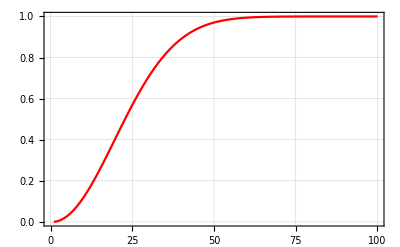

```mathematica
ListLinePlot[P,PlotStyle->RGBColor[1.,0.,0.],PlotTheme->"Detailed"]
```